# Задача 1. Барьерные свойства нанопластин слоистых силикатов

Нанопластины однослойного ММТ толщиной 1 нм и латеральным размером 200 нм однородно распределили в барьерной полимерной пленке толщиной 40 мкм, обеспечив одинаковую ориентацию нанопластин параллельно плоскости пленки. Рассчитать параметры такой барьерной пленки для следующих случаев:

Как зависит от объемной доли нанопластин в композитной полимерной пленке значение ее электрической прочности при условии, что электрическая прочность одного слоя ММТ – 12 В и электрическая прочность полимера – 40 кВ/мм? Какова величина электрической прочности такой барьерной пленки при объемной доле нанопластин 2%?

Как будут отличаться проницаемости по кислороду двух барьерных пленок с одинаковой объемной долей ММТ, в одну из которых ввели однослойные нанопластины ММТ, в другую - двухслойные нанопластины ММТ?

Во сколько раз однородное введение однослойных нанопластин ММТ c объемной долей 1,0% в полимерную пленку снижает ее проницаемость по кислороду, если коэффициент диффузии кислорода в полимере изотропен и ММТ непроницаем для кислорода?

## Решение

#### Пункт 1

Схема пленки:

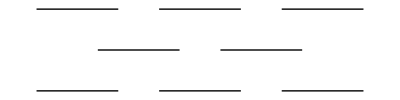

```mathematica
Graphics[{
Line[{{0,0},{2,0}}],
Line[{{3,0},{5,0}}],
Line[{{6,0},{8,0}}],
Line[{{1.5,1},{3.5,1}}],
Line[{{4.5,1},{6.5,1}}],
Line[{{0,2},{2,2}}],
Line[{{3,2},{5,2}}],
Line[{{6,2},{8,2}}]
}]
```

Известные парамаетры в задаче

Толщина слоя:

```mathematica
h=Quantity[1,"Nanometers"];
```

Латеральный размер:

```mathematica
r=Quantity[200,"Nanometers"]/2;
```

Толщина пленки:

```mathematica
H=Quantity[40,"Micrometers"];
```

Электрическая прочность одного слоя ММТ:

```mathematica
epr0=Quantity[40,("Kilowatts")/("Millimeters")];
```

Объемная доля нанопластин:

```mathematica
ϕ=0.02;
```

Количество слоев:

N=(H ϕ)/h

Расстояние между слоями:

d=H/N=h/ϕ

Из условия задачи, прочность ММТ составляет 12 В/нм, прочность полимерной пленки - 0.04 В/нм. Таким образом электроны не пойдут через пластины ММТ. Длина пути диффундирующей частицы между слоями:

l=√(r^2+d^2)=√(r^2+h^2/ϕ^2)

Суммарный путь диффундирующей частицы:

L=N l=(H ϕ)/h √(r^2+h^2/ϕ^2)=H √(1+r^2/h^2 ϕ^2)

Отсюда электрическая прочность:

E_пр=E_пр^0 √(1+r^2/h^2 ϕ^2)

Для ϕ=2% имеем:

```mathematica
n=(H*ϕ)/h;
d=H/n;
l=√(r^2+d^2);
L=n l;
epr2=epr0*L/H
```

89.4427 kW/mm

#### Пункт 2

-Graphics-

В случае двухслойных ММТ количество пластинок уменьшится вдвое, поскольку теперь каждая двуслойная плстинка будет занимать в два раза больше места по высоте. Тогда значение электриеской проницаемости будет:

N=(H ϕ)/(2 h)

d=H/N=(2h)/ϕ

l=√(r^2+d^2)=√(r^2+(4 h^2)/ϕ^2)

L=N l

```mathematica
n=(H*ϕ)/(2 h);
d=H/n;
l=√(r^2+d^2);
L=n l;
epr2=epr0*L/H
```

56.5685 kW/mm

#### Пункт 3

Все то же самое, что и в пункте 1, но ϕ=1%:

```mathematica
ϕ=0.01;
n=(H*ϕ)/h;
d=H/n;
l=√(r^2+d^2);
L=n l;
epr2=epr0*L/H
```

56.5685 kW/mm